```mathematica
f1x=Abs[Sin[6 x]]^3-Cos[5 E^x];
f2x=1/(1+25 x^2)-Sin[20 x];
```

```mathematica
FFT[y_]:=Module[{n,min,supp,,temp,string,reversestring,number,anumber,bnumber,w,i,j,k},
n=Length[y];
(*记录补足的最小的2次幂*)
min=0;
While[n≠1,n=Ceiling[n/2];min++];
(*生成补足2的次幂的列表*)
For[supp=y;i=Length[y]+1,i≤2^min,i++,supp=Append[supp,0]];
(*Print[supp];*)
(*序数重排*)
temp=Table[i,{i,0,2^min-1}];
string=IntegerString[temp,2,min];
reversestring=StringReverse[string];
(*用数组number记录序数重排后的顺序*)
number=Table[FromDigits[reversestring[[i]],2],{i,1,2^min}];
(*离散傅里叶变换，FFT*)
For[i=1,i≤min,i++,
w=E^(-2*Pi*I/(2^i));
For[j=1,j≤2^(min-i),j++,
For[k=1,k≤2^(i-1),k++,
(*Print[{number[[k+(j-1)*2^i]],number[[k+(j-1)*2^i+2^(i-1)]]}]*)
(*原位计算*)
anumber=number[[k+(j-1)*2^i]]+1;
bnumber=number[[k+(j-1)*2^i+2^(i-1)]]+1;
supp[[bnumber]]*=w^(k-1);
supp[[anumber]]+=supp[[bnumber]];
supp[[bnumber]]=supp[[anumber]]-2*supp[[bnumber]];
(*number[[k+(j-1)*2^i+2^(i-1)]]*=w^(k-1);
number[[k+(j-1)*2^i]]+=number[[k+(j-1)*2^i+2^(i-1)]];
number[[k+(j-1)*2^i+2^(i-1)]]=number[[k+(j-1)*2^i]]-2*number[[k+(j-1)*2^i+2^(i-1)]];*)
]]];
supp
]
```

```mathematica
DFT[y_]:=Module[{n,supp,k,min},
n=Length[y];
supp=Table[0,{i,1,n}];
For[k=1,k≤n,k++,
supp[[k]]=Sum[y[[j]]*E^(-2*Pi*(j-1)*(k-1)*I/n),{j,1,n}]
];
supp
];
```

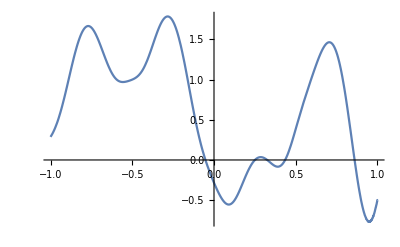

```mathematica
(*插值多项式，牛顿*)
n=40;
t1=Table[N[-Cos[(2 i+1) Pi/(2 n+2)],15],{i,0,n}];
y1=f1x/.x->t1;
For[i=2,i≤n+1,i++,
For[j=n+1,j>=i,j--,
y1[[j]]=(y1[[j]]-y1[[j-1]])/(t1[[j]]-t1[[j-i+1]]);
]
];
fx=y1[[n+1]];
For[i=n+1,i≥2,i--,
fx=y1[[i-1]]+(x-t1[[i-1]])*fx;
];
Plot[fx,{x,-1,1}]
```

{20.7372930838393924,-11.3600849794598487,-4.97132786866462928,2.13369949603962441,-13.2632468970686636,-5.15098215022980472,1.1043591733332903,7.91400838160934224,2.68845874015562102,-0.68829187819088142,5.13629668546286361,-0.79878543675596096,-3.87156139643414845,0.07404584132230987,0.91971635914456243,0.03463380601825783,-0.23832800139959208,-0.00179726620872417,-0.40269043535378483,-0.00093281508821233,0.85828243496972773,-0.00093281508821233,-0.40269043535378483,-0.00179726620872417,-0.23832800139959208,0.03463380601825783,0.91971635914456243,0.07404584132230987,-3.87156139643414845,-0.79878543675596096,5.13629668546286361,-0.68829187819088142,2.68845874015562102,7.91400838160934224,1.1043591733332903,-5.15098215022980472,-13.2632468970686636,2.13369949603962441,-4.97132786866462928,-11.3600849794598487}

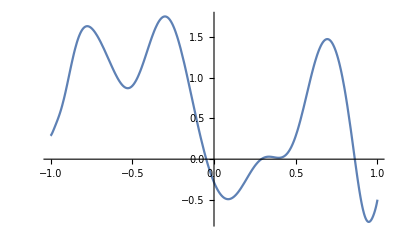

```mathematica
(*生成插值节点*)
n=20;
y=Table[N[Cos[k Pi/n],20],{k,0,n}];
Do[AppendTo[y,y[[n-i+2]]],{i,2,n}];
(*生成插值节点处函数值*)
z=f1x/.x->y;
(*傅里叶变换*)
r=Re[DFT[z]]
(*生成插值多项式*)
f2=r[[1]]/(2 n);
For[i=2,i≤n,i++,f2+=r[[i]]/n *ChebyshevT[i-1,x]];
f2+=r[[n+1]]/(2 n) *ChebyshevT[n,x];
(*绘制函数图像*)
Plot[f2,{x,-1,1}]
```

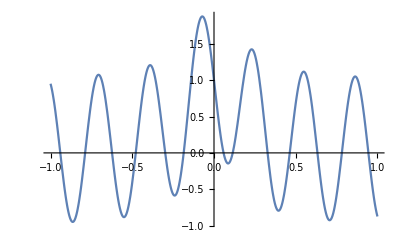
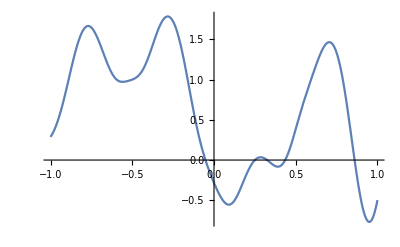
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[f2x,{x,-1,1}],Plot[fx,{x,-1,1}],Plot[f2,{x,-1,1}]}
```